# Lights at the edges, all nodes donate per tick, nodes have a limited capacity

```mathematica
NotebookDirectory[]
```

/home/jovillal/git/redes/

Represent a graph as a list of it nodes, each node a list {m_j,{n_j1,n_j2,…,n_jN_j}}; with m_j∈ℕ^+ an integer (the amount of marbles at node m); {n_j1,n_j2,…,n_jN} the list of neighbors of node m.
When ω_(j k)==0 or Sin[ω_(j k) t+ϕ_(j k)]≥ 0 marbles can leave the node, here ω_(j k) is a frequency, and ϕ_(j k) is a phase associated to the link that connects nodes j and k.
Given a network, the rules of the simulation are that at every tick:
	■ A node tries to pass one of its marbles to one of its neighbors (chosen randomly). 
	■ A marble is passed if ω_(j k)==0∨Sin[ω_(j k) t+ϕ_(j k)]≥ 0, otherwise the marble stays. 
	■ A marble is passed if the receiving node has enough space left to receive all incoming marbles, otherwise no marbles are passed. Each node has capacity  K (same for all nodes).

```mathematica
M=10^2;
S=40;
T=300;
ω=Table[0,{i,M},{j,M}];
ϕ=Table[0,{i,M},{j,M}];
```

So far, forget about lights.

## Functions

## Auxiliaries

eCR[m, i,j] takes a matrix m and exchanges columns and rows i and j.

```mathematica
eCR[am_?MatrixQ,column_Integer,row_Integer]:=Block[{ret=am},
ret[[{column,row}]]=ret[[{row,column}]];
{ret[[All,column]],ret[[All,row]]}={ret[[All,row]],ret[[All,column]]};
ret]
```

sortByOut[m] takes an adjacency matrix and sorts it in a way that VertexOutDegree[AdjacencyGrapg[sortByOut[m]]] is sorted from greater to less, this is equivalent to saying that the first node has the highest out degree and the last node has the smallest.

```mathematica
sortByOut[am_?MatrixQ/;Length[am]==Length[Transpose[am]]]:=Module[
{out=Total/@am,new=am,i,ex},
Do[
If[out[[i]]<Max[out[[i+1;;-1]]],
new=eCR[new,i,i+FirstPosition[out[[i+1;;-1]],Max[out[[i+1;;-1]]]][[1]]];
out=Total/@new;]
,{i,Length[am]-1}];
new
];
sortByOut[_]:=Print["sortByOut input is not a matrix or a square matrix."]
```

sortByIn[m] takes an adjacency matrix and sorts it in a way that VertexInDegree[AdjacencyGrapg[sortByIn[m]]] is sorted from greater to less, this is equivalent to saying that the first node has the highest in degree and the last node has the smallest.

```mathematica
sortByIn[am_?MatrixQ/;Length[am]==Length[Transpose[am]]]:=Module[
{in=Total/@Transpose[am],new=am,i,ex},
Do[
If[in[[i]]<Max[in[[i+1;;-1]]],
new=eCR[new,i,i+FirstPosition[in[[i+1;;-1]],Max[in[[i+1;;-1]]]][[1]]];
in=Total/@Transpose[new];]
,{i,Length[am]-1}];
new
];
sortByIn[_]:=Print["sortByIn input is not a matrix or a square matrix."]
```

remove[g,mrb] takes a graph g as  defined by graphToNet and a list of lists mrb that represents the marble state in graph g and returns a list of integers, where the integer at position i is 0 if no marble can exit or one of the neighbors of node i.

```mathematica
remove[g_,mrb_List(*This is marbles[[-1]]*)]:=Module[{}, (*make this work with lists*)
Table[If[g[[i,2]]≠{}&&mrb[[i]]≠{},RandomChoice[g[[i,2]]],0],{i,Length[g]}]
]
```

add[g,out,mrb] takes a graph g as  defined by graphToNet, a list of integers out (output from remove), a list of lists mrb that represents the marble state in graph g and returns a list of integers, where the integer at position i is one of the neighbors of node i.

```mathematica
add[g_List,inter_List/;inter==ConstantArray[0,Length[inter]],mrb_List(*This is marbles[[-1]]*)]:=mrb
add[g_List,inter_List,mrb_List(*This is marbles[[-1]]*)]:=Module[{nn=Length[inter],marb,i,out=mrb,input},
input=Table[If[inter[[i]]==0,0,RandomChoice[mrb[[i]]]],{i,nn}];
For[i=1,i≤nn,i++,
If[inter[[i]]≠0,
(*Print[i];
Print[inter[[i]]];*)
marb=RandomChoice[out[[i]]];
(*Print[marb];*)
out=ReplacePart[out,inter[[i]]->Append[out[[inter[[i]]]],marb]];
(*Print[out];*)
out=Delete[out,{i,Position[out[[i]],marb][[1,1]]}];
(*Print[out];*)
]];
out
];
```

add[g,out,mrb,tp] takes a graph g as  defined by graphToNet, a list of integers out (output from remove), a list of lists mrb that represents the marble state in graph g and returns a list of integers, where the integer at position i is 0 if no marble can exit or one of the neighbors of node i.

```mathematica
add[g_List,inter_List/;inter==ConstantArray[0,Length[inter]],mrb_List(*This is marbles[[-1]]*),tp_Integer]:=mrb
add[g_List,inter_List,mrb_List(*This is marbles[[-1]]*),tp_Integer]:=Module[{nn=Length[inter],marb,i,out=mrb,input},
input=Table[If[inter[[i]]==0,0,RandomChoice[mrb[[i]]]],{i,nn}];
For[i=1,i≤nn,i++,
If[inter[[i]]≠0,
(*Print[i];
Print[inter[[i]]];*)
marb=RandomChoice[out[[i]]];
(*Print[marb];*)
out=ReplacePart[out,inter[[i]]->Append[out[[inter[[i]]]],marb]];
(*Print[out];*)
out=Delete[out,{i,Position[out[[i]],marb][[1,1]]}];
(*Print[out];*)
]];
If[Not[AllTrue[Length/@out,#≤tp&]],
input=Position[Length/@out,x_/;x>tp]//Flatten;
add[g,inter/.MapThread[Rule,{input,ConstantArray[0,Length[input]]}],mrb,tp]
,
out]
];
```

fillWith[marbles] takes an integer and returns an array of size M with a list of integers m_i at position i, such that ∑_i Length[m_i]==marbles and Length[m_i]≃Length[m_j] for all places.

```mathematica
fillWith[marbles_Integer]:=Module[{int=Floor[marbles/M],float=Mod[marbles,M],ret,count=1},
ret=RandomSample[ConstantArray[int,M]+Join[ConstantArray[1,float],ConstantArray[0,M-float]]];
Table[If[ret[[i]]==0,{},count=count+ret[[i]];Range[count-ret[[i]],count-1]],{i,M}]
]
```

padTally[l, n] takes a list of pairs ordered by the first element and returns a list of length n of the form {{0,p_0},{1,p_1},…,{n-1,p_(n-1)}} where p_i=0 or p_i==l[[j,2]] if l[[j,1]]==i+1.

```mathematica
padTally[l_,n_]:=l/;Length[l]≥n;
padTally[l_,n_]:=Block[{ret},
ret=ReplacePart[ConstantArray[0,n],MapThread[Rule,{l[[All,1]]+1,l[[All,2]]}]];
{Range[n]-1,ret}//Transpose
];
```

## Main functions

graphToNet[graph, ini,order] takes a graph (Mathematica style) and returns a list of elements {{m_i},{n_(j 1),n_(j 2),…,n_(j N_j)}}; with {m_i} the set of packages in the node, and j∈{1,…, N} (N the number of nodes in the graph), n_(j s) the s-th outer neighbour of node j.  The elements are ordered by default according to their outdegree (the first node has the biggest outdegree).
ini can be one of the following:
	• a list of two integers {a,n}, this would put a marbles on node n and no marbles on the other nodes.
	• a list of integers of length N that represents the initial distribution of marbles
order is optional, it determines the order of the elements according to their the out degree 
	• if order is ommited or order≡"Out"  (or whatever else) elements are ordered according to their outdegree (the first node has the biggest outdegree).
	• if order≡"In"  elements are ordered according to their indegree (the first node has the biggest indegree).

```mathematica
graphToNet[g_Graph,ini:{a_,n_}]:=Module[{nei},
nei=sortByOut[Normal[AdjacencyMatrix[g]]];
nei=Flatten[Position[#,1]]&/@nei;
ReplacePart[{{},#}&/@nei,{n,1}->Range[a]]
];
graphToNet[g_Graph,ini_List]:=Module[{nei},
nei=sortByOut[Normal[AdjacencyMatrix[g]]];
nei=Flatten[Position[#,1]]&/@nei;
Transpose[{ini,nei}]
]/;Length[ini]==VertexCount[g];
graphToNet[g_Graph,ini:{a_,n_},"Out"]:=graphToNet[g,{a,n}];
graphToNet[g_Graph,ini_List,"Out"]:=graphToNet[g,ini];
graphToNet[g_Graph,ini:{a_,n_},"In"]:=Module[{nei},
nei=sortByIn[Normal[AdjacencyMatrix[g]]];
nei=Flatten[Position[#,1]]&/@nei;
ReplacePart[{{},#}&/@nei,{n,1}->Range[a]]
];
graphToNet[g_Graph,ini_List,"In"]:=Module[{nei},
nei=sortByIn[Normal[AdjacencyMatrix[g]]];
nei=Flatten[Position[#,1]]&/@nei;
Transpose[{ini,nei}]
]/;Length[ini]==VertexCount[g];
```

netEvolve[graph,T] takes a graph (represented as previously described), with N nodes,  and implements the rule described above for T ticks, there is no maximum number of marbles per node. It returns a list E where every element represents the state of the graph at time t. For each time t, there are n (equal to the number of nodes in graph) elements that contain the marbles present in each node. This is E[[t,m]] gives a list with the marbles present at time t in node m.
This version assumes ω_(j k)=ϕ_(j k)=0

```mathematica
netEvolve[graph_List,T_Integer]:=Module[
{marbles=graph[[All,1]],n=Length[graph]},
NestList[add[graph,remove[graph,#],#]&,marbles,T]
]
```

netEvolve[graph,T,top] takes a graph (represented as previously described), with N nodes, and two integers T and top, and implements the rule described above for T ticks, top defines the maximum number of marbles per node. It returns a list E where every element represents the state of the graph at time t. For each time t, there are n (equal to the number of nodes in graph) elements that contain the marbles present in each node. This is E[[t,m]] gives a list with the marbles present at time t in node m.
This version assumes ω_(j k)=ϕ_(j k)=0

```mathematica
netEvolve[graph_List,T_Integer,top_Integer]:=Module[
{marbles=graph[[All,1]],n=Length[graph]},
NestList[add[graph,remove[graph,#],#,top]&,marbles,T]
]
```

netEvolve[graph,ω,ϕ,T,top] takes a graph (represented as previously described), with N nodes, and two integers T and top, and implements the rule described above for T ticks, top defines the maximum number of marbles per node. It returns a list E, this being an M×T matrix where every row has the number of marbles  of its corresponding node for each tick (this is, element e_(m,t) is the number of marbles of node m at tick t).
ω determines ω_(j k) and ϕ defines ϕ_(j k).
ω must be a matrix such that ω_(j k)→ω[[j,k]]
ϕ must be a matrix such that ϕ_(j k)→ϕ[[j,k]]

```mathematica
netEvolve[graph_List,ω_?MatrixQ,ϕ_?MatrixQ,T_Integer,top_Integer]:=Module[
{marbles={graph[[All,1]]},add,t=0,remove,n=Length[graph]},
(*remove goes over graph and returns a list of integers, the integer is 0 at position i if no marbel can leave node i or the number of the node where the marble is going.
If there is no space at any node, it returns an array of 0*)
remove[g_]:=Module[{ret=ConstantArray[0,n],i,out},
If[AllTrue[#>= top&/@marbles[[-1]],#&],Return[ret]];
For[i=1,i≤n,i++,
If[g[[i,2]]≠{},
out=RandomChoice[g[[i,2]]];
If[ω[[i,out]]==0∨Sin[ω[[i,out]] t+ϕ[[i,out]]]>0,
ret=ReplacePart[ret,i->out]]
]];
(*Print["\tret is ",ret];*)
ret
];
(*add takes the output from remove and builds the new marble distribution, checking if the receiving node can handle the load. If inter is an array of 0, it does nothing*)
add[inter_List/;inter==ConstantArray[0,n]]:=marbles[[-1]];
add[inter_List]:=Module[{out=ConstantArray[0,n],i,kill,tst,input=inter},
For[i=1,i≤n,i++,
If[input[[i]]≠0&&marbles[[-1]][[i]]≥1,
out[[i]]=out[[i]]-1;
out[[input[[i]]]]=out[[input[[i]]]]+1;,
0];
];
tst=marbles[[-1]]+out;
(*Print["\tout before check is ",out];
Print["\tresult would be ",tst];*)
(*now check if the nodes are all below the top limit*)
While[!AllTrue[#≤ top&/@tst,#&],
kill=#->0&/@(Position[tst,x_/;x>top]//Flatten);
input=input/.kill;
For[out=ConstantArray[0,n];i=1,i≤n,i++,
If[input[[i]]≠0&&marbles[[-1]][[i]]≥1,
out[[i]]=out[[i]]-1;
out[[input[[i]]]]=out[[input[[i]]]]+1;,
0];
];
tst=marbles[[-1]]+out;
];
(*Print["\tresult is ",tst];*)
tst
];
Do[
(*Print[remove[graph]];
Print[add[remove/@graph]];*)
AppendTo[marbles,add[remove[graph]]];
t++;
(*Print[t]*)
,T
];
marbles
]
```

netEvolveJ[graph,ω,ϕ,T,top] takes a graph (represented as previously described), with N nodes, and two integers T and top, and implements the rule described above for T ticks, top defines the maximum number of marbles per node. It returns a list of two lists {E,J} with E a M×T matrix where every row has the number of marbles  of its corresponding node for each tick (this is, element e_(m,t) is the number of marbles of node m at tick t); and J a list of T elements where j_t is the number of marbles that where moved within the network in tick t.
ω determines ω_(j k) and ϕ defines ϕ_(j k).
ω must be a matrix such that ω_(j k)→ω[[j,k]]
ϕ must be a matrix such that ϕ_(j k)→ϕ[[j,k]]

```mathematica
netEvolveJ[graph_List,ω_?MatrixQ,ϕ_?MatrixQ,T_Integer,top_Integer]:=Module[
{marbles={{graph[[All,1]],0}},add,t=0,remove,n=Length[graph],j=0},
(*remove goes over graph and returns a list of integers, the integer is 0 at position i if no marbel can leave node i or the number of the node where the marble is going.*)
remove[g_]:=Module[{ret=ConstantArray[0,n],i,out},
If[AllTrue[#>= top&/@marbles[[-1,1]],#&],Return[ret]];
For[i=1,i≤n,i++,
If[g[[i,2]]≠{},
out=RandomChoice[g[[i,2]]];
If[ω[[i,out]]==0∨Sin[ω[[i,out]] t+ϕ[[i,out]]]>0,
ret=ReplacePart[ret,i->out]]
]];
(*Print["\tret is ",ret];*)
ret
];
(*add takes the output from remove and builds the new marble distribution, checking if the receiving node can handle the load.
It modifies j according. If inter is an array of 0, it does nothing*)
add[inter_List/;inter==ConstantArray[0,n]]:={marbles[[-1,1]],0};
add[inter_List]:=Module[{out=ConstantArray[0,n],i,kill,tst,input=inter},
j=0;
For[i=1,i≤n,i++,
If[input[[i]]≠0&&marbles[[-1,1]][[i]]≥1,
j++;
out[[i]]=out[[i]]-1;
out[[input[[i]]]]=out[[input[[i]]]]+1;,
0];
];
tst=marbles[[-1,1]]+out;
(*Print["\tout before check is ",out];
Print["\tresult would be ",tst];*)
(*now check if the nodes are all below the top limit*)
While[!AllTrue[#≤ top&/@tst,#&],
j=0;
kill=#->0&/@(Position[tst,x_/;x>top]//Flatten);
input=input/.kill;
For[out=ConstantArray[0,n];i=1,i≤n,i++,
If[input[[i]]≠0&&marbles[[-1,1]][[i]]≥1,
j++;
out[[i]]=out[[i]]-1;
out[[input[[i]]]]=out[[input[[i]]]]+1;,
0];
];
tst=marbles[[-1,1]]+out;
];
(*Print["\tresult is ",tst];*)
{tst,j}
];

Do[
(*Print[remove[graph]];
Print[add[remove/@graph]];*)
AppendTo[marbles,add[remove[graph]]];
t++;
(*Print[t]*)
,T
];
marbles
]
```

## Graphs

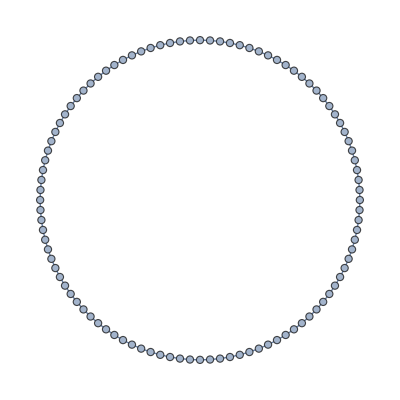

```mathematica
circle=CycleGraph[M]
```

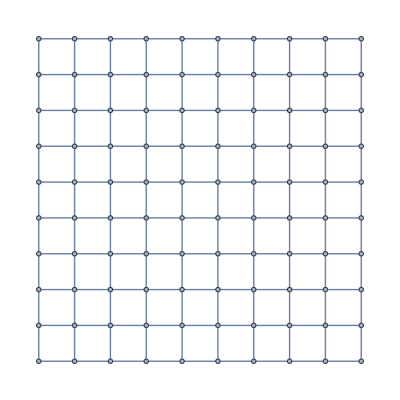

```mathematica
grid=GridGraph[{√M,√M}]
```

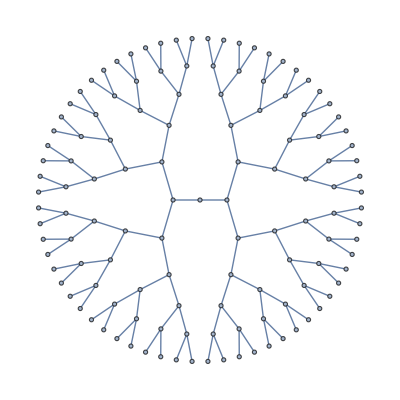

```mathematica
tree=CompleteKaryTree[Round[Log[1+M]/Log[2]]]
```

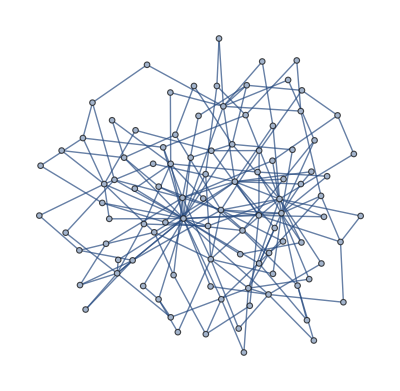

```mathematica
SeedRandom[1234];
scaleFree=RandomGraph[BarabasiAlbertGraphDistribution[M,2]]
```

```mathematica
VertexDegree[scaleFree]
```

{27,12,12,8,4,11,6,13,9,6,3,4,8,5,14,9,7,6,7,3,3,3,3,3,7,3,2,5,4,2,2,3,8,4,4,4,2,4,4,3,4,2,4,3,5,2,2,2,2,2,4,2,3,2,3,3,3,3,3,3,4,2,2,3,2,2,3,2,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,3,2,2,2,2,2,2,3,2,2,2,2}

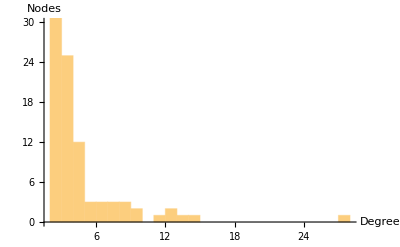

```mathematica
Histogram[VertexDegree[scaleFree],PlotRange->{{2,28},{0,30}},AxesLabel->{"Degree","Nodes"}]
```

## Distance Plots

Make a plot of (<l>)^2/T versus t (?).

distanceTo1[m, evol, g] takes an integer m (a marble id), a list evol that is the output from netEvolve, and another list g that represents the graph used in producing evol; g should be equivalent to  graph[[All,2]] with graph the output from graphToNet.
It returns a list with Length[evol] integers where distanceTo1[m, evol, g][[t]] represents the distance between node 1 and marble m at time t. The distance is the geodesic distance through the graph.

```mathematica
distanceTo1[n_Integer?Positive,evol_List,glist_List]:=Module[
{g=Table[Thread[Rule[i,glist[[i]]]],{i,Length[glist]}],distances=Position[evol,n][[All,2]]},
g=GraphDistanceMatrix[Graph[Range[Length[g]],Flatten[g]]];
g[[#,1]]&/@distances
]
```

distanceBetween[{m_1,m_2}, evol, g] takes two integers m_1 and m_2 (both marble ids), a list evol that is the output from netEvolve, and another list g that represents the graph used in producing evol; g should be equivalent to  graph[[All,2]] with graph the output from graphToNet.
It returns a list with Length[evol] integers where distanceBetween[{m_1,m_2}, evol, g][[t]] represents the distance between marble m_1 and marble m_2 at time t. The distance is the geodesic distance through the graph.

```mathematica
distanceBetween[{n1_Integer?Positive,n2_Integer?Positive},evol_List,glist_List]:=Module[
{g=Table[Thread[Rule[i,glist[[i]]]],{i,Length[glist]}],distances=Transpose[{Position[evol,n1][[All,2]],Position[evol,n2][[All,2]]}]},
g=GraphDistanceMatrix[Graph[Range[Length[g]],Flatten[g]]];
Table[g[[Sequence@@distances[[i]]]],{i,Length[evol]}]
]
```

## Circle

```mathematica
circlenet=graphToNet[circle,{100,1}];
```

```mathematica
marbles=netEvolve[circlenet,2 GraphDiameter[circle]^2];
```

```mathematica
sij=distanceBetween[#,marbles,circlenet[[All,2]]]&/@Flatten[Table[{i,j},{i,9},{j,i+1,10}],1];
```

```mathematica
sijM=Mean/@Transpose[sij];
```

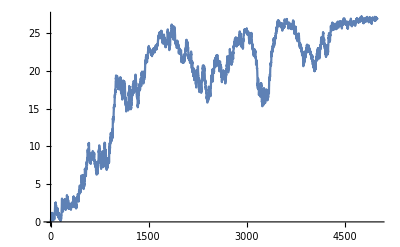
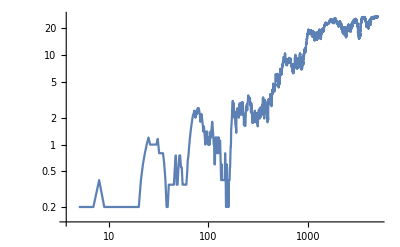

```mathematica
{ListLinePlot[sijM],ListLogLogPlot[sijM,Joined->True]}
```

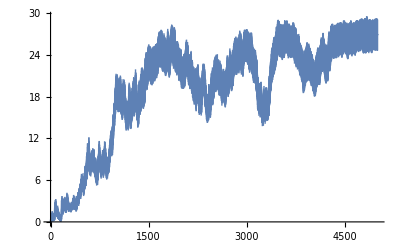
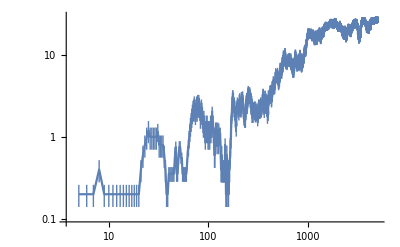

```mathematica
{ListLinePlot[MeanAround/@Transpose[sij]],ListLogLogPlot[MeanAround/@Transpose[sij],Joined->True]}
```

## Grid

make it start in one of the corners

```mathematica
gridnet=graphToNet[grid,{100,1}];
```

```mathematica
marbles=netEvolve[gridnet,2 GraphDiameter[grid]^2];
```

```mathematica
sij=distanceBetween[#,marbles,gridnet[[All,2]]]&/@Flatten[Table[{i,j},{i,9},{j,i+1,10}],1];
```

```mathematica
sijM=Mean/@Transpose[sij];
```

```mathematica
sijMA=MeanAround/@Transpose[sij];
```

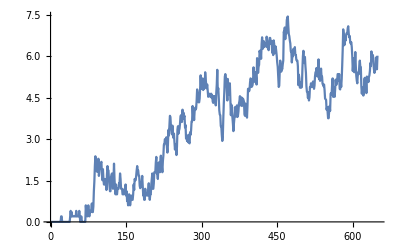
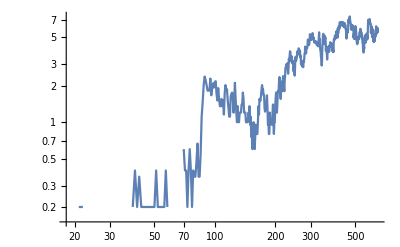

```mathematica
{ListLinePlot[sijM],ListLogLogPlot[sijM,Joined->True]}
```

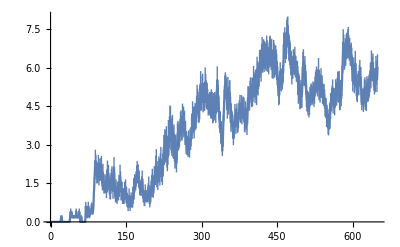
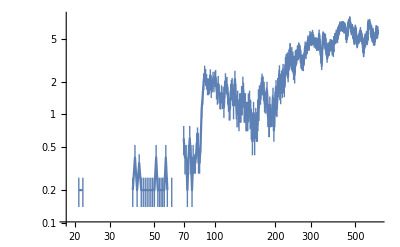

```mathematica
{ListLinePlot[sijMA],ListLogLogPlot[sijMA,Joined->True]}
```

## Tree

make it start in one of the leaves

```mathematica
treenet=graphToNet[tree,{100,1}];
```

```mathematica
treenet[[2]]
```

{{},{5,6,63}}

```mathematica
marbles=netEvolve[gridnet,2 GraphDiameter[grid]^2];
```

```mathematica
sij=distanceBetween[#,marbles,gridnet[[All,2]]]&/@Flatten[Table[{i,j},{i,9},{j,i+1,10}],1];
```

```mathematica
sijM=Mean/@Transpose[sij];
```

```mathematica
sijMA=MeanAround/@Transpose[sij];
```

```mathematica
{ListLinePlot[sijM],ListLogLogPlot[sijM,Joined->True]}
```

{-Graphics-,-Graphics-}

```mathematica
{ListLinePlot[sijMA],ListLogLogPlot[sijMA,Joined->True]}
```

{-Graphics-,-Graphics-}

```mathematica
sfnet=graphToNet[scaleFree,fillWith[2M]];
```

```mathematica
marbles=netEvolve[sfnet,1300,5];
```

```mathematica
marbles//Length
```

1301

```mathematica
distanceBetween[{1,2},marbles,sfnet[[All,2]]];
```

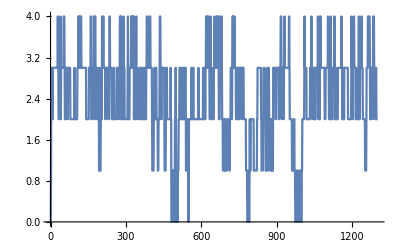

```mathematica
ListLinePlot[%]
```

4

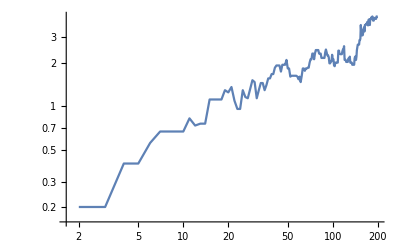

```mathematica
GraphDistanceMatrix[scaleFree]//Max
```

```mathematica
sij[[1]][[2]]
```

{0,1,0,0,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,3,1,1,1,1,1,1,1,1,1,1,2,3,3,2,2,2,2,3,3,3,3,3,3,3,3,3,3,4,3,3,1,0,0,0,0,0,1,1,1,2,2,2,2,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,0,0,0,1,1,0,0,0,0,1,2,2,2,2,2,2,2,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,0,0,1,2,2,2,2,2,2,2,2,3,2,2,2,3,3,2,2,2,2,2,3,4,4,5,5,5,5,5,7,7,7,7,7,7,7,7,7,6,6,6,6,6,6,7,6,6,6,7,7,6,5,5,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,7,6,6,4,4,4,4,4,4,2,2,2,2,2,2,2,2,2,3,3,3,4,4,5,5,5,3,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,2,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,4,4,4,4,4,4,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,6,6,6,7,7,7,7,7,8,8,9,11,11,11,11,11,11,10,10,10,11,11,11,11,11,11,11,11,11,11,10,10,10,11,11,11,11,11,11,11,12,12,12,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,15,15,15,15,15,15,15,15,17,17,17,17,16,16,16,15,14,14,14,14,14,14,14,14,14,14,14,15,15,16,16,17,17,18,17,17,17,17,17,17,18,18,19,19,19,19,19,20,20,20,20,20,21,21,21,21,21,21,21,21,21,21,21,21,22,22,23,23,23,23,23,23,23,23,23,23,23,22,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,25,25,25,26,26,26,27,27,26,25,25,26,26,26,26,27,27,26,27,27,27,27,29,28,28,29,29,28,28,29,29,29,28,29,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,27,29,29,29,29,29,29,29,29,29,29,29,29,29,30,30,30,29,29,29,29,29,29,29,29,29,29,30,30,30,30,30,30,30,30,30,30,30,32,32,31,31,31,31,31,31,31,31,30,30,30,30,30,29,29,30,30,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,30,30,30,30,30,30,30,30,30,30,30,30,28,28,28,28,28,28,28,28,28,26,26,25,26,25,25,25,25,25,25,25,25,25,25,25,25,25,26,26,27,27,27,27,27,27,28,28,28,28,28,27,28,28,28,28,28,28,28,28,28,28,29,28,28,28,28,28,28,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,28,28,28,28,28,28,28,29,29,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,31,31,31,31,31,32,34,34,34,33,33,33,32,32,32,32,32,32,32,32,32,32,32,32,32,32,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,31,31,31,32,33,33,33,33,33,33,33,33,33,33,33,33,33,32,32,32,32,33,33,33,34,34,34,34,34,34,34,34,34,34,34,34,34,32,32,32,32,32,31,31,32,32,32,31,32,33,33,32,31,31,31,31,31,32,31,31,31,30,30,30,30,29,29,29,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,29,30,30,30,30,30,31,31,31,31,31,31,31,31,31,30,29,29,29,29,29,28,29,29,29,29,29,28,27,27,27,27,26,27,28,28,28,27,26,25,25,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,25,26,25,25,25,24,24,24,25,25,24,23,23,23,23,23,23,22,22,22,22,21,21,21,22,22,21,21,20,20,20,20,20,20,20,20,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,19,19,19,19,18,18,18,17,17,16,16,15,17,16,16,15,15,15,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,13,13,12,12,12,12,12,12,12,12,12,12,12,14,14,14}

```mathematica
Length/@sij
```

{9,8,7,6,5,4,3,2,1,0}

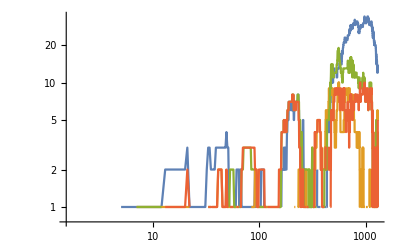

```mathematica
ListLogLogPlot[{distanceBetween[{1,2},marbles,circlenet[[All,2]]],distanceBetween[{3,4},marbles,circlenet[[All,2]]],distanceBetween[{1,3},marbles,circlenet[[All,2]]],distanceBetween[{1,4},marbles,circlenet[[All,2]]]},Joined->True]
```

```mathematica
GraphDistanceMatrix[circle]//Max
```

50

```mathematica
gridnet=graphToNet[grid,fillWith[2M]];
```

```mathematica
marbles=netEvolve[gridnet,1300,5];
```

```mathematica
distanceBetween[{1,2},marbles,gridnet[[All,2]]];
```

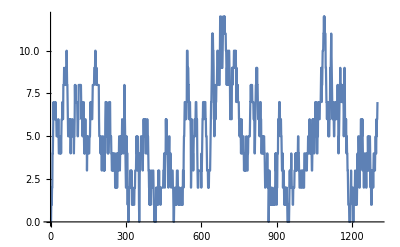

```mathematica
ListLinePlot[%]
```

```mathematica
GraphDistanceMatrix[grid]//Max
```

14

```mathematica
hypernet=graphToNet[hyper,fillWith[2M]];
```

```mathematica
marbles=netEvolve[hypernet,1300,5];
```

```mathematica
distanceBetween[{1,2},marbles,hypernet[[All,2]]];
```

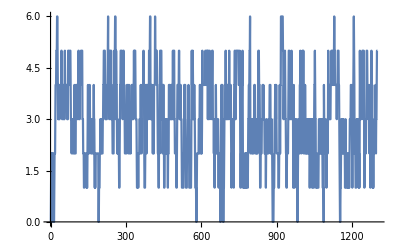

```mathematica
ListLinePlot[%]
```

```mathematica
GraphDistanceMatrix[hyper]//Max
```

6